# Test and Filter Runs

n: number of stars
NS: number of simulations
R: virial radius
Isolated System

### Logs

```mathematica
Print[$RunNumber]
```

500

```mathematica
Print[script`path]
```

/home/cesarg/git/workspace/nbody6/isolated/scripts/FilterAndTest

```mathematica
logstream = OpenWrite[
FileNameJoin[{script`path, "nbstatus" <> ToString[$RunNumber] <> ".log"}],
FormatType->OutputForm
]
```

OutputStream[…]

```mathematica
Write[logstream, "Begin log ...."];
```

## Initialization

```mathematica
{$MachineName,$Version}
```

{tars,12.1.0 for Linux x86 (64-bit) (March 18, 2020)}

```mathematica
AppendTo[$Path,Environment["MYGITDIR"]];
```

```mathematica
Get["AstroTools`nbody6`"]
```

```mathematica
Get["AstroTools`Utilities`"]
```

```mathematica
$ConfiguredKernels = 
 List[SubKernels`LocalKernels`LocalMachine[30, 
   Rule[SubKernels`LocalKernels`LowerPriority, True]]]
```

{SubKernels`LocalKernels`LocalMachine[30,SubKernels`LocalKernels`LowerPriority→True]}

```mathematica
$SAVEMXQ=False
```

False

```mathematica
resultsPath=FileNameJoin[{Environment["MYGITDIR"],"workspace","nbody6","isolated","n"<>ToString[$RunNumber],"NSX-R1","results"}]
```

/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results

```mathematica
SetDirectory[resultsPath]
```

/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results

```mathematica
FileNames[]
```

{run-1,run-10,run-100,run-101,run-102,run-103,run-104,run-105,run-106,run-107,run-108,run-109,run-11,run-110,run-111,run-112,run-113,run-114,run-115,run-116,run-117,run-118,run-119,run-12,run-120,run-121,run-122,run-123,run-124,run-125,run-126,run-127,run-128,run-129,run-13,run-130,run-131,run-132,run-133,run-134,run-135,run-136,run-137,run-138,run-139,run-14,run-140,run-141,run-142,run-143,run-144,run-145,run-146,run-147,run-148,run-149,run-15,run-150,run-151,run-152,run-153,run-154,run-155,run-156,run-157,run-158,run-159,run-16,run-160,run-161,run-162,run-163,run-164,run-165,run-166,run-167,run-168,run-169,run-17,run-170,run-171,run-172,run-173,run-174,run-175,run-176,run-177,run-178,run-179,run-18,run-180,run-181,run-182,run-183,run-184,run-185,run-186,run-187,run-188,run-189,run-19,run-190,run-191,run-192,run-193,run-194,run-195,run-196,run-197,run-198,run-199,run-2,run-20,run-200,run-201,run-202,run-203,run-204,run-205,run-206,run-207,run-208,run-209,run-21,run-210,run-211,run-212,run-213,run-214,run-215,run-216,run-217,run-218,run-219,run-22,run-220,run-221,run-222,run-223,run-224,run-225,run-226,run-227,run-228,run-229,run-23,run-230,run-231,run-232,run-233,run-234,run-235,run-236,run-237,run-238,run-239,run-24,run-240,run-241,run-242,run-243,run-244,run-245,run-246,run-247,run-248,run-249,run-25,run-250,run-251,run-252,run-253,run-254,run-255,run-256,run-257,run-258,run-259,run-26,run-260,run-261,run-262,run-263,run-264,run-265,run-266,run-267,run-268,run-269,run-27,run-270,run-271,run-272,run-273,run-274,run-275,run-276,run-277,run-278,run-279,run-28,run-280,run-281,run-282,run-283,run-284,run-285,run-286,run-287,run-288,run-289,run-29,run-290,run-291,run-292,run-293,run-294,run-295,run-296,run-297,run-298,run-299,run-3,run-30,run-300,run-31,run-32,run-33,run-34,run-35,run-36,run-37,run-38,run-39,run-4,run-40,run-41,run-42,run-43,run-44,run-45,run-46,run-47,run-48,run-49,run-5,run-50,run-51,run-52,run-53,run-54,run-55,run-56,run-57,run-58,run-59,run-6,run-60,run-61,run-62,run-63,run-64,run-65,run-66,run-67,run-68,run-69,run-7,run-70,run-71,run-72,run-73,run-74,run-75,run-76,run-77,run-78,run-79,run-8,run-80,run-81,run-82,run-83,run-84,run-85,run-86,run-87,run-88,run-89,run-9,run-90,run-91,run-92,run-93,run-94,run-95,run-96,run-97,run-98,run-99}

## Delete invalid runs

```mathematica
If[Not[DirectoryQ["temp"]],
Import["!../run2end.sh","String"];goodFiles=FileNameJoin[First[#]]&/@GatherBy[StringSplit[Import["goodRuns.log"][[All,2]],"/"],#[[-2]]&];dirs=DirectoryName/@goodFiles;dirsToDelete=Complement[Select[FileNames[],DirectoryQ],Part[StringSplit[#,$PathnameSeparator]&/@dirs,All,2]];dirsToDelete=Flatten[StringCases[dirsToDelete,"run-"~~__]];Print[dirsToDelete//Short];Print[dirsToDelete//Length];(*Table[Style[Import[StringTemplate["!tail -n 2 ``/output"][dirsToDelete[[j]]],"String"],If[OddQ[j],Blue,Brown]],{j,Length@dirsToDelete}]//ColumnForm*)
If[Length[dirsToDelete]≠0,
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete,
Print["Nothing to delete"]];
CreateDirectory["temp"];
runsToMove=FileNames["run*"];
CopyFile[#,"./temp/"<>FileBaseName[#]]&/@runsToMove;DeleteDirectory[#,DeleteContents->True]&/@runsToMove;DeleteFile["goodRuns.log"];
]
```

{run-1,run-100,run-102,run-103,run-104,run-107,run-109,run-115,run-117,run-119,run-12,run-125,run-127,run-128,run-129,run-13,run-132,run-133,run-136,run-137,run-140,run-143,run-149,run-150,run-151,run-152,run-153,run-155,run-158,run-16,run-160,run-164,run-168,run-17,run-170,run-175,run-176,run-177,run-180,run-183,run-186,run-19,run-194,run-197,run-199,run-200,run-204,run-207,run-210,run-214,run-215,run-22,run-220,run-221,run-224,run-226,run-23,run-230,run-235,run-236,run-238,run-239,run-24,run-242,run-243,run-244,run-245,run-246,run-248,run-25,run-251,run-254,run-255,run-256,run-257,run-259,run-261,run-264,run-269,run-271,run-272,run-273,run-276,run-278,run-281,run-282,run-286,run-292,run-294,run-298,run-3,run-300,run-31,run-33,run-34,run-39,run-4,run-43,run-45,run-47,run-48,run-5,run-50,run-51,run-53,run-54,run-56,run-57,run-58,run-61,run-64,run-65,run-67,run-7,run-72,run-76,run-79,run-82,run-83,run-84,run-86,run-87,run-9,run-90,run-91,run-93,run-95,run-96,run-99}

129

```mathematica
Write[logstream, "goo shape run directories moved to temp"]
```

### MOVE runs from TEMP

```mathematica
(**** IMPORTANT: run this section only in ByGroup mode ****)
```

```mathematica
filesToMove=Take[FileNames["temp/run*"],UpTo[50]]
```

{temp/run-10,temp/run-101,temp/run-105,temp/run-106,temp/run-108,temp/run-11,temp/run-110,temp/run-111,temp/run-112,temp/run-113,temp/run-114,temp/run-116,temp/run-118,temp/run-120,temp/run-121,temp/run-122,temp/run-123,temp/run-124,temp/run-126,temp/run-130,temp/run-131,temp/run-134,temp/run-135,temp/run-138,temp/run-139,temp/run-14,temp/run-141,temp/run-142,temp/run-144,temp/run-145,temp/run-146,temp/run-147,temp/run-148,temp/run-15,temp/run-154,temp/run-156,temp/run-157,temp/run-159,temp/run-161,temp/run-162,temp/run-163,temp/run-165,temp/run-166,temp/run-167,temp/run-169,temp/run-171,temp/run-172,temp/run-173,temp/run-174,temp/run-178}

```mathematica
If[filesToMove==={},
goodRuns=Take[FileNames["good-runs/run*"],UpTo[50]];
Print@Length[goodRuns];badRuns=Take[FileNames["bad-runs/run*"],UpTo[Max[0,50-Length[goodRuns]]]];Print@Length[badRuns];CopyFile[#,"./"<>FileBaseName[#]]&/@Join[goodRuns,badRuns];DeleteDirectory[#,DeleteContents->True]&/@Join[goodRuns,badRuns];Import["!../run2end.sh","String"];
Quit[]
]
```

```mathematica
CopyFile[#,"./"<>FileBaseName[#]]&/@filesToMove
```

{/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-10,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-101,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-105,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-106,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-108,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-11,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-110,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-111,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-112,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-113,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-114,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-116,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-118,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-120,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-121,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-122,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-123,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-124,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-126,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-130,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-131,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-134,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-135,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-138,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-139,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-14,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-141,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-142,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-144,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-145,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-146,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-147,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-148,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-15,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-154,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-156,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-157,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-159,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-161,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-162,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-163,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-165,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-166,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-167,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-169,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-171,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-172,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-173,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-174,/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results/run-178}

```mathematica
DeleteDirectory[#,DeleteContents->True]&/@filesToMove
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Import["!../run2end.sh","String"]
```

```mathematica
Write[logstream, "moved upt to 50 files to proccess"]
```

### n–body parameters

```mathematica
(*
numberOfStars=380;
nb["S0"]=0.3(numberOfStars/1000)^(1/3)
nb["nMAX"]=2.(numberOfStars)^(1/2)
*)
```

```mathematica
FilePrint["../create-ini.sh"]
```

#!/bin/bash

echo "[`date`] Start"

mkdir ./results/

cd results/
for filenumber in {1..300..1}
do
	mkdir "./run-$filenumber/"
  	cat << EOF > ./run-$filenumber/ini.dat
1 20.0
500 1 10 $RANDOM 48 1
0.02 0.01 0.24 2.0 1.0 1601.0 1.0E-03 1 0.5
0 0 1 0 1 0 0 0 0 0
0 0 0 0 0 0 0 0 0 6
0 0 0 0 0 0 0 0 0 0
0 0 0 0 0 0 0 0 0 1
0 0 0 0 0 0 0 0 0 0
2.0E-05 0.001 0.2 1.0 1.0E-06 0.001
2.3 50.0 0.2 0 0 0.002 0 0
0.5 0 0 0 0.5
EOF

done

cd ..
echo `pwd`
echo "[`date`] End"
echo "time elapsed: $SECONDS"
echo all done

```mathematica
strCreateFile=Import["../create-ini.sh","Table"]
```

{{#!/bin/bash},{},{echo,[`date`] Start},{},{mkdir,./results/},{},{cd,results/},{for,filenumber,in,{1..300..1}},{do},{mkdir,./run-$filenumber/},{cat,<<,EOF,>,./run-$filenumber/ini.dat},{1,20.},{500,1,10,$RANDOM,48,1},{0.02,0.01,0.24,2.,1.,1601.,0.001,1,0.5},{0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,6},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0},{0.00002,0.001,0.2,1.,1.×10^-6,0.001},{2.3,50.,0.2,0,0,0.002,0,0},{0.5,0,0,0,0.5},{EOF},{},{done},{},{cd,..},{echo,`pwd`},{echo,[`date`] End},{echo,time elapsed: $SECONDS},{echo,all,done},{},{}}

```mathematica
pos=Position[strCreateFile,"$RANDOM"][[1,1]];
numberOfStars=strCreateFile[[pos,1]]
nbodyStep=Floor@(strCreateFile[[pos+1,5]])
maxNbodyTime=Floor@(strCreateFile[[pos+1,6]]-nbodyStep)
```

500

1

1600

### Other global variables

#### Data

```mathematica
goodFiles=FileNameJoin[First[#]]&/@GatherBy[StringSplit[Import["goodRuns.log"][[All,2]],"/"],#[[-2]]&];
```

```mathematica
dirs=DirectoryName/@goodFiles;
```

```mathematica
runmax=Length[dirs]
```

50

```mathematica
If[!FileExistsQ["nbody6-data.mx"]
,
Print["Loading from source ..."];
data=ReadOutput/@goodFiles;
If[$SAVEMXQ,DumpSave["nbody6-data.mx",data]];
,
Print["Loading from MX ..."];
Get["nbody6-data.mx"];
]//AbsoluteTiming
```

Loading from source ...

ReadList::readn: Invalid real number found when reading from «1».

General::stop: Further output of «1» will be suppressed during this calculation.

{20.031,Null}

```mathematica
parameters=data[[All,1]];
```

```mathematica
parameters//Length
```

50

```mathematica
data=data[[All,2]];
```

```mathematica
lengthOfRuns=Tally[Length/@data]
```

{{1601,50}}

#### Parameters

```mathematica
(* NOTE 1: parameters V^*, T^*, M^* are different for each run *)
(* NOTE 2: $MeanMass numberOfStats ≈ $MassScale *)
parameters[[All,4]]
```

{0.677,0.758,0.73,0.739,0.679,0.686,0.777,0.781,0.713,0.758,0.775,0.773,0.722,0.678,0.777,0.717,0.718,0.744,0.719,0.685,0.663,0.653,0.785,0.767,0.751,0.717,0.736,0.692,0.668,0.737,0.743,0.744,0.669,0.715,0.698,0.701,0.749,0.704,0.724,0.708,0.707,0.745,0.734,0.652,0.685,0.737,0.745,0.673,0.7,0.794}

```mathematica
{$LengthScale,$MassScale,$SpeedScale,$TimeScale,$MeanMass,$SU}=Mean[parameters]
```

{1.,429.768,1.35776,0.72204,0.8588,4.4×10^7}

```mathematica
$EnergyScale=$MassScale ($SpeedScale)^2
```

792.283

```mathematica
$DensityScale=$MassScale/($LengthScale)^3
```

429.768

```mathematica
(* in units of Msun/pc^3*)
ρSunNeighborPhysical=0.09;
ρForClusterDisruptionPhysical=0.08;
```

```mathematica
(* in units of n-body units *)
ρSunNeighbor=ρSunNeighborPhysical/$DensityScale;
ρForClusterDisruption=ρForClusterDisruptionPhysical/$DensityScale;
```

```mathematica
(* checking units *)
ρSunNeighbor
```

0.000209415

```mathematica
(* mean density in nbody units *)
$MeanDensity=1./(4/3Pi(1)^3)
```

0.238732

```mathematica
(* mean density physical Msun/pc^3 *)
$MeanDensity $DensityScale
```

102.6

```mathematica
(* Max elpased time for evolution in MY*)
maxNbodyTime*$TimeScale
```

1155.26

```mathematica
(* INITIAL TIME = 0 -> following nbody6 *)
timeArray=Range[0,maxNbodyTime,nbodyStep];
(* log step array: 0 time at -1 *)
log10TimeArray1=N@Prepend[Log10[Rest[timeArray]],0];
log10TimeArrayScaled1=N@Prepend[Log10[Rest[$TimeScale timeArray]],0];
```

```mathematica
Length/@{timeArray,log10TimeArray1,log10TimeArrayScaled1}
```

{1601,1601,1601}

## run cpu timings

```mathematica
Directory[]
```

/home/cesarg/git/workspace/nbody6/isolated/n500/NSX-R1/results

```mathematica
timingFiles=FileNames["run*/timings"];
timingFiles//Short
```

{run-101/timings,run-105/timings,run-106/timings,run-108/timings,run-10/timings,run-110/timings,run-111/timings,run-112/timings,run-113/timings,run-114/timings,run-116/timings,run-118/timings,run-11/timings,run-120/timings,run-121/timings,run-122/timings,run-123/timings,run-124/timings,run-126/timings,run-130/timings,run-131/timings,run-134/timings,run-135/timings,run-138/timings,run-139/timings,run-141/timings,run-142/timings,run-144/timings,run-145/timings,run-146/timings,run-147/timings,run-148/timings,run-14/timings,run-154/timings,run-156/timings,run-157/timings,run-159/timings,run-15/timings,run-161/timings,run-162/timings,run-163/timings,run-165/timings,run-166/timings,run-167/timings,run-169/timings,run-171/timings,run-172/timings,run-173/timings,run-174/timings,run-178/timings}

```mathematica
timeStrings=Cases[Import[#],{"real",_}][[1,2]]&/@timingFiles;
timeStrings//Short
```

{0m50.164s,1m3.560s,1m23.476s,1m9.326s,1m28.298s,1m6.072s,1m13.366s,1m0.591s,1m17.330s,1m16.360s,1m4.776s,1m36.664s,0m50.350s,0m57.961s,1m5.193s,1m8.608s,1m4.688s,1m5.853s,0m51.278s,1m6.206s,1m13.416s,1m8.952s,1m19.259s,1m8.772s,1m22.385s,1m10.685s,0m47.364s,1m7.504s,1m38.044s,1m22.799s,1m7.218s,1m53.156s,0m46.119s,0m39.823s,1m12.625s,0m57.458s,0m43.853s,1m19.600s,2m16.546s,1m31.158s,0m47.477s,0m52.989s,0m58.905s,1m28.069s,1m15.327s,1m6.443s,0m52.583s,0m41.666s,0m53.212s,0m59.678s}

```mathematica
timeElapsedStringToSeconds[string_]:=(60#1+#2)&@@ToExpression[StringSplit[string,"m"|"s"]]
```

```mathematica
timings=timeElapsedStringToSeconds/@timeStrings;
```

```mathematica
If[#>60,Quantity[#/60,"Minutes"],Quantity[#,"Seconds"]]&@Mean[timings]
```

Set::write: Tag «12» in «1» is Protected.

General::stop: Further output of «1» will be suppressed during this calculation.

SetDelayed::write: Tag «11» in «1» is Protected.

General::stop: Further output of «1» will be suppressed during this calculation.

1.14774 min

```mathematica
If[#>60,Quantity[#/60,"Minutes"],Quantity[#,"Seconds"]]&@StandardDeviation[timings]
```

18.3354 s

## n–body results

### Mean rhalf

```mathematica
meanRhalf=Mean/@DeleteCases[Transpose[data[[All,All,1]]],$Failed,{2}];
```

```mathematica
meanRhalfAndTime=Transpose[{timeArray,meanRhalf}];
```

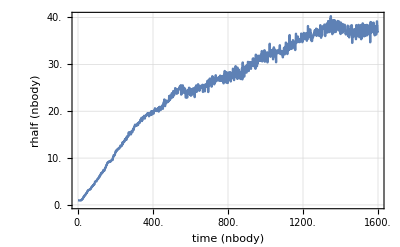

```mathematica
meanRhalfAndTimePlot=ScaledListPlot[meanRhalfAndTime,{$TimeScale,$LengthScale},
FrameLabel->{{"rhalf (nbody)","rhalf (pc)"},{"time (nbody)","time (My)"}},
"ShowAllScales"->True]
```

### Mean rdens

```mathematica
meanRdens=Mean/@DeleteCases[Transpose[data[[All,All,3]]],$Failed,{2}];
```

```mathematica
meanRdensAndTime=Transpose[{timeArray,meanRdens}];
```

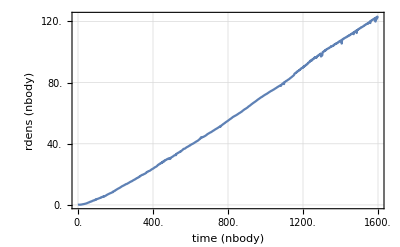

```mathematica
meanRdensAndTimePlot=ScaledListPlot[meanRdensAndTime,{$TimeScale,$LengthScale},
FrameLabel->{{"rdens (nbody)","rdens (pc)"},{"time (nbody)","time (My)"}},"ShowAllScales"->True]
```

## Loading Data

#### Load from OUT3 or MX

```mathematica
(* 8 values: id, pos, vel, mass *)
(* 8 bytes each one *)
```

```mathematica
(numberOfStars*maxNbodyTime*runmax*8*8)/(1024*1024*1024. nbodyStep)
```

2.38419

```mathematica
snapshots=All;
```

```mathematica
(*snapshots=Range[1,maxNbodyTime,10];*)
```

```mathematica
Write[logstream, "computing particles.mx ...."]
```

```mathematica
(* Check also: "particles.bin" *)
If[!FileExistsQ["particles.mx"]
	,
	Print[TimeAndMem[]];
	(*While[Kernels[] == {}, 
		kernels = LaunchKernels[];
		];*)
	kernels = LaunchKernels[];
	Write[logstream, kernels];
	Print["Kernels: ", kernels];
	SetSharedVariable[dirs];
	ParallelEvaluate[AppendTo[$Path, Environment["MYGITDIR"]]];
	ParallelEvaluate[SetDirectory[resultsPath]];
	ParallelNeeds["AstroTools`nbody6`"];
	ParallelNeeds["AstroTools`Utilities`"];
	(particles = 
		Transpose@
		ParallelTable[
			SetDirectory[dirs[[i]]];
			Print["DIR: ", dirs[[i]]];
			{bodys,xs,vs,name} = Flatten[ReadOUT3["OUT3","Snapshots" -> snapshots], 1];
			xs=Partition[#,3]&/@xs;
			vs=Partition[#,3]&/@vs;
			ResetDirectory[]; 
			{bodys,xs,vs,name}
			,
			{i,1,Length[dirs]}]);
	
	Print["Closing kernels ..."];
	CloseKernels[];

	(*-- SAVE to a MX file --*)
	If[$SAVEMXQ,
		Print["Saving data to MX ... "];
		Print[TimeAndMem[]];
		DumpSave["particles.mx", particles];
		Print[TimeAndMem[]];
	];

	(*-- SAVE to a BIN file --*)
	(* BinarySerializeSave[particles,"particles.bin"]; // AbsoluteTiming *)
	
	,
	
	(*-- Get file from MX --*)
	Print["Loading MX ..."];
	Get["particles.mx"];
] // AbsoluteTiming
```

11:40:04 mem:179.618MB

Kernels: {KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

DIR: ./run-101/

DIR: ./run-106/

DIR: ./run-10/

DIR: ./run-111/

DIR: ./run-113/

DIR: ./run-116/

DIR: ./run-11/

DIR: ./run-121/

DIR: ./run-123/

DIR: ./run-126/

DIR: ./run-131/

DIR: ./run-135/

DIR: ./run-139/

DIR: ./run-142/

DIR: ./run-145/

DIR: ./run-147/

DIR: ./run-14/

DIR: ./run-156/

DIR: ./run-159/

DIR: ./run-161/

DIR: ./run-163/

DIR: ./run-165/

DIR: ./run-166/

DIR: ./run-167/

DIR: ./run-169/

DIR: ./run-171/

DIR: ./run-172/

DIR: ./run-173/

DIR: ./run-174/

DIR: ./run-178/

DIR: ./run-112/

DIR: ./run-105/

DIR: ./run-108/

DIR: ./run-110/

DIR: ./run-114/

DIR: ./run-120/

DIR: ./run-122/

DIR: ./run-130/

DIR: ./run-134/

DIR: ./run-138/

DIR: ./run-141/

DIR: ./run-144/

DIR: ./run-146/

DIR: ./run-148/

DIR: ./run-157/

DIR: ./run-15/

DIR: ./run-162/

DIR: ./run-118/

DIR: ./run-124/

DIR: ./run-154/

Closing kernels ...

{227.149,Null}

```mathematica
Write[logstream, "particles.mx done!"]
```

```mathematica
(* --- serial computation ---
(particles=
Transpose@
Table[SetDirectory[dirs[[i]]];
Print["DIR: ", dirs[[i]]];
{bodys,xs,vs,name}=Flatten[ReadOUT3["OUT3","Snapshots"->All],1];
xs=Partition[#,3]&/@xs;
vs=Partition[#,3]&/@vs;
ResetDirectory[]; 
{bodys,xs,vs,name}
,{i,1,Length[dirs]}]);//AbsoluteTiming *)
```

#### Mem information

```mathematica
TimeAndMem[]
```

11:43:51 mem:10.3762GB

```mathematica
(*PrintArrayInfo[particles]*)
```

```mathematica
DeleteOuts[500]
```

session mem: 10.3762GB

No Out[] greater than 500MB

```mathematica
$numberOfRunsStatus=Dimensions[particles][[2]]
```

50

## Filtering Invalid Data

### Indexes To Extract Data

```mathematica
nbIndexes=Table[Range[maxNbodyTime/nbodyStep+1],{runmax}];
```

```mathematica
nbIndexes//Dimensions
```

{50,1601}

```mathematica
nbIndexes[[1]]//Short
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1039,1040,1041,1042,1043,1044,1045,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1072,1073,1074,1075,1076,1077,1078,1079,1080,1081,1082,1083,1084,1085,1086,1087,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1144,1145,1146,1147,1148,1149,1150,1151,1152,1153,1154,1155,1156,1157,1158,1159,1160,1161,1162,1163,1164,1165,1166,1167,1168,1169,1170,1171,1172,1173,1174,1175,1176,1177,1178,1179,1180,1181,1182,1183,1184,1185,1186,1187,1188,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1200,1201,1202,1203,1204,1205,1206,1207,1208,1209,1210,1211,1212,1213,1214,1215,1216,1217,1218,1219,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234,1235,1236,1237,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247,1248,1249,1250,1251,1252,1253,1254,1255,1256,1257,1258,1259,1260,1261,1262,1263,1264,1265,1266,1267,1268,1269,1270,1271,1272,1273,1274,1275,1276,1277,1278,1279,1280,1281,1282,1283,1284,1285,1286,1287,1288,1289,1290,1291,1292,1293,1294,1295,1296,1297,1298,1299,1300,1301,1302,1303,1304,1305,1306,1307,1308,1309,1310,1311,1312,1313,1314,1315,1316,1317,1318,1319,1320,1321,1322,1323,1324,1325,1326,1327,1328,1329,1330,1331,1332,1333,1334,1335,1336,1337,1338,1339,1340,1341,1342,1343,1344,1345,1346,1347,1348,1349,1350,1351,1352,1353,1354,1355,1356,1357,1358,1359,1360,1361,1362,1363,1364,1365,1366,1367,1368,1369,1370,1371,1372,1373,1374,1375,1376,1377,1378,1379,1380,1381,1382,1383,1384,1385,1386,1387,1388,1389,1390,1391,1392,1393,1394,1395,1396,1397,1398,1399,1400,1401,1402,1403,1404,1405,1406,1407,1408,1409,1410,1411,1412,1413,1414,1415,1416,1417,1418,1419,1420,1421,1422,1423,1424,1425,1426,1427,1428,1429,1430,1431,1432,1433,1434,1435,1436,1437,1438,1439,1440,1441,1442,1443,1444,1445,1446,1447,1448,1449,1450,1451,1452,1453,1454,1455,1456,1457,1458,1459,1460,1461,1462,1463,1464,1465,1466,1467,1468,1469,1470,1471,1472,1473,1474,1475,1476,1477,1478,1479,1480,1481,1482,1483,1484,1485,1486,1487,1488,1489,1490,1491,1492,1493,1494,1495,1496,1497,1498,1499,1500,1501,1502,1503,1504,1505,1506,1507,1508,1509,1510,1511,1512,1513,1514,1515,1516,1517,1518,1519,1520,1521,1522,1523,1524,1525,1526,1527,1528,1529,1530,1531,1532,1533,1534,1535,1536,1537,1538,1539,1540,1541,1542,1543,1544,1545,1546,1547,1548,1549,1550,1551,1552,1553,1554,1555,1556,1557,1558,1559,1560,1561,1562,1563,1564,1565,1566,1567,1568,1569,1570,1571,1572,1573,1574,1575,1576,1577,1578,1579,1580,1581,1582,1583,1584,1585,1586,1587,1588,1589,1590,1591,1592,1593,1594,1595,1596,1597,1598,1599,1600,1601}

```mathematica
nbLenIndexes=Length/@nbIndexes
```

{1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601}

### Incomplete runs

```mathematica
particles//Dimensions
```

{4,50}

```mathematica
Length/@particles[[4]]//Union
```

{1598,1599,1600,1601}

```mathematica
(* delete runs that have not complete data *)
maxtimes=Length/@particles[[4]]
```

{1601,1600,1601,1601,1601,1600,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1600,1600,1599,1600,1601,1601,1601,1601,1599,1599,1601,1600,1600,1600,1599,1600,1601,1601,1599,1600,1601,1601,1600,1598,1601,1601,1601,1601,1601,1601,1600,1601,1601,1601}

```mathematica
delPos1=Position[maxtimes,x_/;x<Max[maxtimes]]
```

{{2},{6},{17},{18},{19},{20},{25},{26},{28},{29},{30},{31},{32},{35},{36},{39},{40},{47}}

```mathematica
delPos1//Length
```

18

#### FIX: Delete complete runs

```mathematica
Extract[dirs,delPos1]
```

{./run-105/,./run-110/,./run-123/,./run-124/,./run-126/,./run-130/,./run-139/,./run-141/,./run-144/,./run-145/,./run-146/,./run-147/,./run-148/,./run-156/,./run-157/,./run-161/,./run-162/,./run-172/}

```mathematica
dirsToDelete=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,delPos1],All,2]
```

{run-105,run-110,run-123,run-124,run-126,run-130,run-139,run-141,run-144,run-145,run-146,run-147,run-148,run-156,run-157,run-161,run-162,run-172}

```mathematica
dirsToDelete//Length
```

18

```mathematica
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

Opt – Update variables to continue computing

```mathematica
particles//Dimensions
```

{4,50}

```mathematica
dirs=Delete[dirs,delPos1];
runmax=Length[dirs];
particles=Delete[#, delPos1]&/@particles;
nbIndexes=Delete[nbIndexes, delPos1];
nbLenIndexes=Length/@nbIndexes;
parameters=Delete[parameters, delPos1];
```

```mathematica
particles//Dimensions
```

{4,32,1601}

```mathematica
nbIndexes//Length
```

32

```mathematica
parameters//Dimensions
```

{32,6}

```mathematica
PrintArrayInfo[particles]
```

Length: 4 MEM: 6.9054GB

### Particles in the same position

#### TEST

```mathematica
particles[[All,All,All,1;;numberOfStars]]//Dimensions
```

{4,32,1601,500}

```mathematica
Clear[ceros];
If[!FileExistsQ["ceros.mx"],
ceros=Reap[
Do[
Print["run: ", run];
Do[
With[
{pe=TotalPotentialEnergy[particles[[1,run,t,All]],particles[[2,run,t,All]]]},
If[pe==0.,Sow[{run,t}];Print["CERO AT: ", run];Break[]]
]
,{t,1,nbLenIndexes[[run]]}
],
{run,1,runmax}]
];
DumpSave["ceros.mx", ceros]
,
(*-- Get file from MX --*)
	Print["Loading MX ..."];
	Get["ceros.mx"];
];//AbsoluteTiming
```

run: 1

run: 2

run: 3

run: 4

run: 5

run: 6

run: 7

run: 8

run: 9

run: 10

run: 11

run: 12

run: 13

run: 14

run: 15

run: 16

run: 17

run: 18

run: 19

run: 20

run: 21

run: 22

run: 23

run: 24

run: 25

run: 26

run: 27

run: 28

run: 29

run: 30

run: 31

run: 32

{912.043,Null}

```mathematica
ceros[[2]]
```

{}

#### Double check

```mathematica
(*invalid=With[{run=7},Reap[Do[
With[
{pe=TotalPotentialEnergy[particles[[1,run,t,All]],particles[[2,run,t,All]]]},
If[pe==0.,Sow[{run,t}]]
]
,{t,1,nbLenIndexes[[run]]}
]]
];*)
```

```mathematica
(*invalid//Short*)
```

```mathematica
(*With[{run=7, time=1100},
Select[GatherBy[Transpose[{particles[[4,run,time,All]],particles[[2,run,time,All]]}],Last],Length[#]>1&]]*)
```

```mathematica
(*With[
{part1=2,
part2=1,
run=46,
interTime=220
},
vel=Table[{#[part1],#[part2]}&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,run,time,All]],particles[[3,run,time,All]]}]|>),{time,1,nbLenIndexes[[run]],1}];
pos=Table[{#[part1],#[part2]}&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,run,time,All]],particles[[2,run,time,All]]}]|>),{time,1,nbLenIndexes[[run]],1}];

{ListLinePlot[{Norm/@vel[[All,1]],Norm/@vel[[All,2]]},
PlotRange->{{0,1000},{0,100}}],
ListLinePlot[{Norm/@pos[[All,1]],Norm/@pos[[All,2]]},
PlotRange->{{0,1000},{0,50000}},Epilog->InfiniteLine[{{interTime,0},{interTime,1}}]]}
]*)
```

```mathematica
(* testing indexes outside particles range *)
```

```mathematica
(*testing1001=Table[#[1001]&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,2,time,All]],particles[[2,2,time,All]]}]|>),{time,1,nbLenIndexes[[2]],1}];*)
```

```mathematica
(*Position[testimg1001,_Missing]*)
```

```mathematica
(*testing1002=Table[#[1002]&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,2,time,All]],particles[[2,2,time,All]]}]|>),{time,1,nbLenIndexes[[2]],1}];*)
```

```mathematica
(*testing1002[[8]]*)
```

#### FIX 1: Delete complete runs

```mathematica
delPos2=If[ceros[[2]]=={},{},Partition[Union[ceros[[2,1]][[All,1]]],1]];
```

```mathematica
delPos2//Short
```

{}

```mathematica
Extract[dirs,delPos2]
```

{}

```mathematica
dirsToDelete=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,delPos2],All,2]
```

{}

```mathematica
dirsToDelete//Length
```

0

```mathematica
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete;
```

Opt 1 – Delete files to begin from scratch

(* 
	Si dirsToDelete≠0 borrar *.m *.mx 
	generar goodRuns.log y correr nb de nuevo.
*)

FileNames["*.*"]

DeleteFile[#] & /@ FileNames["*.*"]

Opt 2 – Update variables to continue computing

```mathematica
dirs=Delete[dirs,delPos2];
```

```mathematica
runmax=Length[dirs]
```

32

```mathematica
particles//Dimensions
```

{4,32,1601}

```mathematica
particles=Delete[#, delPos2]&/@particles;
```

```mathematica
particles//Dimensions
```

{4,32,1601}

```mathematica
PrintArrayInfo[particles]
```

Length: 4 MEM: 6.9054GB

```mathematica
nbIndexes=Delete[nbIndexes, delPos2];
```

```mathematica
nbIndexes//Length
```

32

```mathematica
nbLenIndexes=Length/@nbIndexes
```

{1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601,1601}

```mathematica
parameters//Dimensions
```

{32,6}

```mathematica
parameters=Delete[parameters, delPos2];
```

```mathematica
parameters//Dimensions
```

{32,6}

#### FIX 2: Delete specific snapshots (ruled out)

```mathematica
(* We will delete data only for snapshots containg equal positions *)
```

delPos3 = ceros[[2, 1]]

particles = Delete[#, delPos3] & /@ particles;

timeIndexes[[1, 450]]

Complement[Range[1000], timeIndexes[[1]]]

timeIndexes = Delete[timeIndexes, delPos3];

Complement[Range[1000], timeIndexes[[1]]]

nbLenIndexes = Length /@ timeIndexes

### Particles with index 0 / position 0.

#### TEST

```mathematica
(* Delete time snaphots of incorrect data with ceros in the position vector. *)
(* Very strange issue from nbody *)
```

```mathematica
delPos4=Position[particles[[4]],0][[All,{1,2}]];
```

```mathematica
delPos4//Short
```

{{1,287},{3,1191},{3,1192},{3,1193},{3,1194},{3,1195},{4,233},{4,492},{5,341},{6,45},{6,57},{6,58},{6,96},{6,572},{8,60},{8,540},{8,910},{8,911},{8,912},{9,34},{9,40},{10,20},{10,179},{10,1098},{10,1099},{10,1100},{10,1101},{14,42},{15,65},{15,184},{15,185},{17,45},{17,638},{18,844},{18,890},{18,891},{18,892},{18,894},{18,895},{18,896},{18,897},{18,898},{18,899},{18,900},{18,901},{18,902},{18,903},{18,904},{18,905},{18,906},{19,83},{19,84},{19,85},{20,264},{20,265},{20,266},{20,1063},{20,1064},{21,101},{21,107},{23,144},{26,297},{26,298},{26,394},{26,395},{26,396},{26,397},{26,444},{26,459},{26,460},{27,34},{29,45},{31,22},{31,30},{32,24},{32,26},{32,44},{32,45},{32,46},{32,199},{32,200},{32,204},{32,205},{32,206},{32,263}}

```mathematica
delPos4[[All,1]]//Union
```

{1,3,4,5,6,8,9,10,14,15,17,18,19,20,21,23,26,27,29,31,32}

```mathematica
delPos4[[All,1]]//Union//Length
```

21

```mathematica
(* NICE runs *)
Complement[Range[runmax],delPos4[[All,1]]//Union]
```

{2,7,11,12,13,16,22,24,25,28,30}

```mathematica
(* Consistent with non missing IDs *)
moreIDS=Table[Position[Complement[Range[numberOfStars],#]&/@particles[[4,run,All,All]],x_/;x≠{},{1}],{run,runmax}];
Position[moreIDS,{}]//Flatten
```

{2,7,11,12,13,16,22,24,25,28,30}

```mathematica
bad=Partition[delPos4[[All,1]]//Union,1];
good=Partition[Position[moreIDS,{}]//Flatten,1];
```

```mathematica
Write[logstream,"bad runs: ",bad]
```

```mathematica
Write[logstream,"good runs: ",good]
```

```mathematica
badRunsDirs=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,bad],All,2]
```

{run-101,run-108,run-10,run-111,run-112,run-114,run-116,run-118,run-122,run-131,run-135,run-138,run-142,run-14,run-154,run-15,run-166,run-167,run-171,run-174,run-178}

```mathematica
goodRunsDirs=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,good],All,2]
```

{run-106,run-113,run-11,run-120,run-121,run-134,run-159,run-163,run-165,run-169,run-173}

```mathematica
If[!DirectoryQ["good-runs"],CreateDirectory["./good-runs"]];
If[!DirectoryQ["bad-runs"],CreateDirectory["./bad-runs"]];
```

```mathematica
CopyDirectory[#,"./good-runs/"<>#]&/@goodRunsDirs;
CopyDirectory[#,"./bad-runs/"<>#]&/@badRunsDirs;
```

```mathematica
DeleteDirectory[goodRunsDirs,DeleteContents->True];
DeleteDirectory[badRunsDirs,DeleteContents->True];
```

## Close

```mathematica
(*Print["len in goodRubs:: ",Length[StringSplit[Import["goodRuns.log","String"],"\n"]]];
Print["len in particles:: ",$numberOfRunsStatus]
If[$numberOfRunsStatus>50,
Import["!../run2end.sh","String"];
Print["deleted: ",FileNames[{"*.m","*.mx"}]];
DeleteFile[#]&/@FileNames[{"*.m","*.mx"}]
]*)
```

```mathematica
Write[logstream, "End succesfully ...."]
```

```mathematica
Close[logstream]
```

/home/cesarg/git/workspace/nbody6/isolated/scripts/FilterAndTest/nbstatus500.log